```mathematica
ClearAll["Global`*"]
$Assumptions= τ ∈ Reals && m∈Reals && n ∈ Reals &&r ∈Reals;
alpha[m_,n_]:= 1/2 KroneckerDelta[0, Abs[m-n]] - 1/4 KroneckerDelta[1, Abs[m-n]] + E^(-(m-n)^2/ 8/Pi/ξ /ξ )/2/Sqrt[2]/Pi/ξ ;
beta [m_,n_]:= Sign[m-n]* ( 1/4 KroneckerDelta[1, Abs[m-n]] - Exp[I*(2τ- Abs[m-n]^2/4/ξ/l)]/2/Sqrt[π ξ l] Exp[- π Abs[m-n]^2/4/l/l ]Sqrt[1-Exp[-π Abs[m-n]^2/4/l/l]]           );
ξ= Sqrt[τ];
l = Sqrt[τ]* Log[τ];
```

```mathematica
BA[m_,n_]:=KroneckerDelta[m,n]-2alpha[n-m,0]+2Re[beta[n-m,0]]
```

```mathematica
G = Simplify[BA[0,2]]
```

-ⅇ^(-1/(2 π τ))/(√2 π √τ)-Re[(ⅇ^(-(π+ⅈ Log[τ]-2 ⅈ τ^2 Log[τ]^2)/(τ Log[τ]^2)) √(1-ⅇ^(-π/(τ Log[τ]^2))))/(√(τ Log[τ]))]/(√π)

General::munfl: Exp[-7543.24-46.4676 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7543.24] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

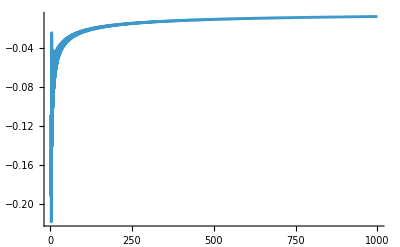

```mathematica
Plot[G,{τ,1,1000},PlotRange->All]
```

```mathematica
Sign[0]
```

0